g2 graph 21b
level 4

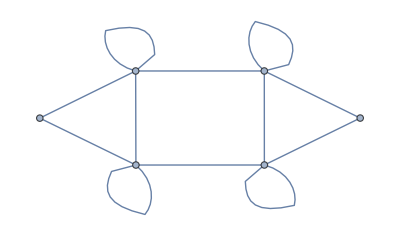

```mathematica
SetDirectory["~/Documents/UNH/Research/code/gen2/graph_21b"];
graph = { {0,1,0,0,0,1},
{1,1,1,0,0,1},
{0,1,1,1,1,0},
{0,0,1,0,1,0},
{0,0,1,1,1,1},
{1,1,0,0,1,1}
 };
AdjacencyGraph[ graph] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt];
CGamma = { {0,aa,0,0,0,bb},
{cc,dd,ee,0,0,ff},
{0,gg,hh,ii,jj,0},
{0,0,kk,0,ll,0},
{0,0,mm,nn,oo,pp},
{qq,rr,0,0,ss,tt}
};
level=4;
q=Exp[2*Pi*I/(3*(4+level))]; (* 2*Pi*I/(3*(4+ level)) *)
```